Setup

```mathematica
Clear[CurveSketchingModule]
CurveSketchingModule[function_,range_]:=Module[
{f=function,r=range},

(*Finding Absolute max and mins*)
maxAndMins = 
x/.Solve[
f'[x]==0,x
]/.{C[1]->0};

(*Finding inflection points*)
inflectionPoints = 
x/.Solve[
f''[x]==0,x
]/.{C[1]->0};

TestingMaxMinValues=
Map[
{#+0.1,#-0.1}&,
maxAndMins
];

TestingInflectionPointValues=
Map[
{#+0.1,#-0.1}&,
inflectionPoints
];

LocMaxMinPointsForFunction=
Map[
Point[
{#,f[#]}
]&,
maxAndMins
];

InflectionPointsForGraphics=
Map[
Point[
{#,f[#]}
]&,
inflectionPoints
];

(*Creating a graph of the function*)
OriginalFunction=
Plot[
f[x],
Prepend[r,x],
PlotStyle->Black
];

NumberLineGraphic=NumberLinePlot[
{
{f'[x]>0&&f''[x]>0},
{f'[x]>0&&f''[x]<0},
{f'[x]<0&&f''[x]<0},
{f'[x]<0&&f''[x]>0},
f'[x]==0||f''[x]==0
}//Evaluate,
Prepend[r,x]//Evaluate,
PlotLegends->
{"++","+-","--","-+"},
PlotStyle->{{Dashed,Red},{Dotted,Magenta},{DotDashed,Blue},{Green}},
Spacings->
0
];

Print[
Show[
OriginalFunction,
Graphics[
{PointSize[0.02],
LocMaxMinPointsForFunction,
InflectionPointsForGraphics
}
]
,NumberLineGraphic
]
];

Print[
"Local Maximum(s)/Minimum(s) at: " 
];

LocMaxMinPointsForFunction=
Apply[
List[#]&,
LocMaxMinPointsForFunction,
{1,1}
];

Print[
Grid[ 
LocMaxMinPointsForFunction
]
];

Print[
"Inflection Point(s) at: " 
];

InflectionPointsForGraphics=
Apply[
List[#]&,
InflectionPointsForGraphics,
{1,1}
];

Print[
Grid[ 
InflectionPointsForGraphics
]
];
]
```

```mathematica
(*Clear[f]
f[x_]:=x^2 E^x*)
```

```mathematica
Clear[f]
f[x_]:=x^5 Log[x]
```

```mathematica
f''[.5]
```

-0.607868

```mathematica
N[9/8-(5 Log[2])/2]
```

-0.607868

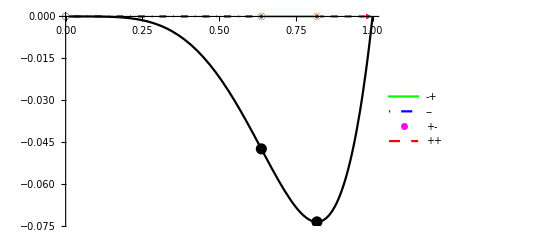

Local Maximum(s)/Minimum(s) at:

{1/ⅇ^(1/5),-1/(5 ⅇ)}

Inflection Point(s) at:

{1/ⅇ^(9/20),-9/(20 ⅇ^(9/4))}

```mathematica
CurveSketchingModule[f,{0,1}]
```